```mathematica
SetDirectory["~/projects/matrix-models-cpp"];
```

```mathematica
Get["./mathematica/lib/lib2.m"];
Get["./mathematica/lib/util.m"];
```

```mathematica
data = Import["./runs/Trials/N9K9/12279703.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rad = {#[[1]], (Total@((#[[2;;$K(($N)^2-1)+1]])^2))}&/@data;
```

```mathematica
σ = StandardDeviation@data[[All, 4]];
```

```mathematica
(2$K(($N)^2-1))/($N)1/Mean[rad[[All, 2]]]
```

29.2928

```mathematica
($K*(($N)^2-1)/2)
```

360

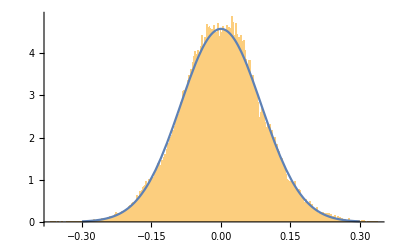

```mathematica
Show[Histogram[data[[All, 6]], 400, PDF],
Plot[PDF[NormalDistribution[0, σ], x], {x, -0.3, 0.3}]]
```

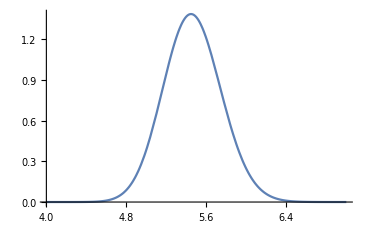

```mathematica
p = Plot[PDF[GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2], x], {x, 4, 7}]
```

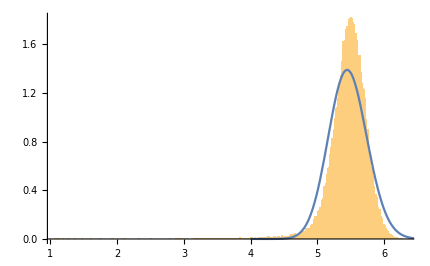

```mathematica
Show[Histogram[rad[[All, 2]], 400, PDF],
p
]
```

```mathematica
Mean@GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2]
```

5.46209

```mathematica
StandardDeviation@GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2]
```

0.287877

```mathematica
Skewness@GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2]//N
```

0.105409

```mathematica
Kurtosis@GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2]//N
```

3.01667

```mathematica
Mean@rad[[All, 2]]
```

5.46209

```mathematica
StandardDeviation@rad[[All, 2]]
```

0.278212

```mathematica
Skewness@rad[[All, 2]]
```

-1.72294

```mathematica
Kurtosis@rad[[All, 2]]
```

15.3749

```mathematica
Mean[GammaDistribution[($K*(($N)^2-1)/2), 2 σ^2]]
```

5.46209

```mathematica
σ=(Mean[rad[[All, 2]]]/($K(($N)^2-1)))^(1/2)
```

0.087099

```mathematica
Mean[rad[[All, 2]]]
```

5.46209

```mathematica
2$K(($N)^2-1)σ^4
```

0.0828733

```mathematica
Variance[rad[[All, 2]]]
```

0.0774021

```mathematica
$K(($N)^2-1)σ^2
```

5.46209

```mathematica
Mean[rad[[All, 2]]]
```

5.46209